Help me make a function for partial derangements. For example 1234 has the 3 partial derangement 1432 and the 2 derangement 1243. Here's another example 4321 is a 4-derangement of 1234 because all places have changed.

Sure! Here's a function that takes a list of integers and an integer n and returns the number of partial derangements of length n of the list: 

Here Derangement[list,n] computes the number of derangements of length n of the list. The function partialDerangements uses the inclusion-exclusion principle to compute the number of partial derangements. 

For example, to find the number of partial derangements of length 3 of the list {1,2,3,4}, you can call: 

which gives the output 3.

Let me know if you have any questions about how this function works!

```mathematica
ClearAll[EnumeratePartialDerangements]
```

```mathematica
EnumeratePartialDerangements[n_,k_]:=Binomial[n,k]Subfactorial[n-k]
```

```mathematica
EnumeratePartialDerangements::usage="Enum"
```

```mathematica
fInformation::usage="fInformation[x] computes xxxx.";
```

A permutation of n distinct, ordered items in which none of the items is in its original ordered position is known as a derangement. If some, but not necessarily all, of the items are not in their original ordered positions, the configuration can be referred to as a partial derangement (Evans et al. 2002, p. 385).

Write a usage message for EnumeratePartialDerangements. Here is how to write a usage message f::usage = "f[x] computes xxxx.";

Here's an example usage message for EnumeratePartialDerangements: 

This message explains what the function does, the meaning of the inputs, and how the function works to compute the output. It also includes the formula used by the function to compute the result. 

Let me know if you have any questions!

```mathematica
EnumeratePartialDerangements::usage = "EnumeratePartialDerangements[n, k] computes the number of partial derangements of length k of n distinct, ordered items. A partial derangement is a permutation in which k items are not in their original order. The function uses the formula Binomial[n, k]Subfactorial[n-k].";
```

```mathematica
square[x_]:=x^2
```

```mathematica
InitializationValue[squarefunction,"Local"]=square
```

square

```mathematica
Initialize[squarefunction]
```

{Global`squarefunction}

```mathematica
squarefunction[3]
```

9

```mathematica
InitializationValue[cubefunction,"Local"]=Function[x,x^3]
```

Function[x,x^3]

```mathematica
Initialize[cubefunction]
```

{Global`cubefunction}

```mathematica
InitializationValue[AlternatingTreeGraph,"Local"]=ResourceFunction["AlternatingTreeGraph"][##]&
```

ResourceFunction[AlternatingTreeGraph][##1]&

```mathematica
Initialize[AlternatingTreeGraph]
```

{Global`AlternatingTreeGraph}

It looks like you are defining two functions squarefunction and cubefunction and initializing them, as well as defining and initializing a function AlternatingTreeGraph using the ResourceFunctionpaclet:ref/ResourceFunction AlternatingTreeGraph.

The InitializationValuepaclet:ref/InitializationValue function is used to set the values of symbols before the main code is evaluated. The syntax is: 

where symbol is the symbol whose value is being set, scope is either "Local" or "Global" to specify the scope of the symbol, and value is the value being assigned to the symbol.

The Initializepaclet:ref/Initialize function is then used to initialize the symbols whose values were set with InitializationValuepaclet:ref/InitializationValue. The syntax is: 

where symbol1, symbol2, etc. are the symbols being initialized.

In this case, squarefunction and cubefunction are both defined as functions that take a single argument and return its square and cube, respectively. AlternatingTreeGraph is defined using a ResourceFunctionpaclet:ref/ResourceFunction that generates an alternating tree graph. 

Let me know if you have any questions!

```mathematica
cubefunction[7]
```

343

```mathematica
g[x_]:=IntegerDigits[x];
```

```mathematica
g[x_Real]:=RealDigits[x];
```

```mathematica
g[___]:={}
```

```mathematica
gPure=Function[input,g[input]]
```

Function[input,g[input]]

```mathematica
g[1337]
```

{1,3,3,7}

```mathematica
gPure[1337]
```

{1,3,3,7}

```mathematica
g[N@Pi]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3},1}

```mathematica
gPure[N@Pi]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3},1}

```mathematica
g["Hello","World"]
```

{}

```mathematica
gPure["Hello","World"]
```

IntegerDigits[Hello]

```mathematica
DownValues[gPure]
```

{}

```mathematica
DownValues[g]
```

{HoldPattern[g[x_Real]]:>RealDigits[x],HoldPattern[g[x_]]:>IntegerDigits[x],HoldPattern[g[___]]:>{}}

```mathematica
g[{1}]/.{HoldPattern[g[x_Real]]:>RealDigits[x],HoldPattern[g[x_]]:>IntegerDigits[x],HoldPattern[g[___]]:>{}}
```

{{1}}

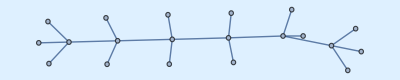

```mathematica
ResourceFunction["AlternatingTreeGraph"][8,Background->LightBlue]
```